# Chapter 2: Closed-System Solution of the 1D Atom from Collision Model

## Author: Bruno Ortega Goes

This section contains the calculations to obtain the analytical formulas presented in Ref. [1] and the plots of important quantities based on these expressions presented in the thesis.

References:	
[1] Maffei, M., Camati, P.A., Auffèves, A., 2022. Closed-System Solution of the 1D Atom from Collision Model. Entropy 24, 151. https://doi.org/10.3390/e24020151

```mathematica
(*Setting the path where the plots are going to be saved.*)
nbdirectory=SetDirectory[NotebookDirectory[]];
PlotsPath=nbdirectory<>"/PlotsChap2/";

Clear[e,g,up,dw]
(*Defining the basis*)
ket[0]=ket[up]=ket[e] =Basis[2,1];
ket[1]=ket[dw] = ket[g] =Basis[2,2];
bra[ket_]:=ket*//cf;
```

## Coherent drive

We chose a resonant drive, i.e. δ=0. This choice is convenient to obtain analytical results because in this regime we have real amplitudes of probability allowing the symbolic computation of the probabilities. The non-resonant case can be dealt with numerical integration.
In all this notebook we set time in terms of decay rate, i.e. γ=1.

For this section we chose 3 different values of the Rabi frequency, going from Ω<<γ to Ω>>γ.

```mathematica
par1 = {δ->0,γ->1,Ω->0.1};
par2 = {δ->0,γ->1,Ω->0.6};
par3 = {δ->0,γ->1,Ω->10};
listofparametersCoherentDrive ={par1,par2,par3};
```

### Coefficients

```mathematica
(*No-photon emission coefficient-- This is the building block for the next coefficients.*)
f0[ϵ_,ζ_,t_]:=Module[{aux,aux2,aux3,arg},
aux= ket[ϵ].MatrixExp[-ⅈ t/2 (aux3 σp.σm-aux2 σy)].ket[ζ]//cf;
aux/.aux2->Ω/.aux3->2(δ - ⅈ γ/2)//cf]

(*Single-photon emission coefficient*)
f1[ϵ_,ζ_,t_,t1_]:=f0[ϵ,g,t-t1]f0[e,ζ,t1]

(*Two-photons emission coefficient*)
f2[ϵ_,ζ_,t_,t2_,t1_]:=f0[ϵ,g,t-t2]f0[e,g,t2-t1]f0[e,ζ,t1]

(*Three-photons emission coefficient*)
f2[ϵ_,ζ_,t_,t3_,t2_,t1_]:=f0[ϵ,g,t-t3]f0[e,g,t3-t2]f0[e,g,t2-t1]f0[e,ζ,t1]
```

Defining the modified Rabi frequency:

```mathematica
ΩB=√((δ-ⅈ γ/2 )^2+Ω^2)
```

√((-(ⅈ γ)/2+δ)^2+Ω^2)

```mathematica
(-(γ+2 ⅈ δ)^2+4 Ω^2)/4//Expand
```

-γ^2/4-ⅈ γ δ+δ^2+Ω^2

```mathematica
(δ-ⅈ γ/2 )^2+Ω^2//Expand
```

-γ^2/4-ⅈ γ δ+δ^2+Ω^2

```mathematica
(-(γ+2 ⅈ δ)^2)/4//Expand
```

-γ^2/4-ⅈ γ δ+δ^2

```mathematica
(δ-ⅈ γ/2 )^2//Expand
```

-γ^2/4-ⅈ γ δ+δ^2

```mathematica
(ⅇ^(-1/4 t (γ+2 ⅈ δ)) Ω Sin[ t ΩB])/ΩB
```

(ⅇ^(-1/4 t (γ+2 ⅈ δ)) Ω Sin[t √((-(ⅈ γ)/2+δ)^2+Ω^2)])/(√((-(ⅈ γ)/2+δ)^2+Ω^2))

```mathematica
f0[e,g,t]//cf
```

(2 ⅇ^(-1/4 t (γ+2 ⅈ δ)) Ω Sin[1/2 t √((-(ⅈ γ)/2+δ)^2+Ω^2)])/(√(-(γ+2 ⅈ δ)^2+4 Ω^2))

```mathematica
(f0[e,g,t]//cf)-((ⅇ^(-1/4 t (γ+2 ⅈ δ)) Ω Sin[ t ΩB/2])/ΩB//cf)//cf
```

0

```mathematica
f0[g,g,t]//cf
```

ⅇ^(-1/4 t (γ+2 ⅈ δ)) (Cos[1/2 t √((-(ⅈ γ)/2+δ)^2+Ω^2)]+((γ+2 ⅈ δ) Sin[1/2 t √((-(ⅈ γ)/2+δ)^2+Ω^2)])/(√(-(γ+2 ⅈ δ)^2+4 Ω^2)))

```mathematica
√(-(γ+2 ⅈ δ)^2+4 Ω^2)-2ΩB//cf
```

0

```mathematica
f0[g,g,t]-ⅇ^(-1/4 t (γ+2 ⅈ δ)) (Cos[1/2 t ΩB]+((γ+2 ⅈ δ) Sin[1/2 t ΩB])/(2ΩB))//cf
```

0

```mathematica
Clear[ΩB]
ⅇ^(-1/4 t (γ+2 ⅈ δ)) (Cos[1/2 t ΩB]+((γ+2 ⅈ δ) Sin[1/2 t ΩB])/(2ΩB))/.δ->0/.ΩB->ⅈ γ/2//cf
((ⅇ^(-1/4 t (γ+2 ⅈ δ)) Ω Sin[ t ΩB/2])/ΩB/.δ->0/.ΩB->ⅈ γ/2)//cf
```

1

(Ω-ⅇ^(-(t γ)/2) Ω)/γ

```mathematica
coeffNoEmissionList=
{f0ge=f0[g,e,t]//cf,
f0eg=f0[e,g,t]//cf};

coeff1photonEmissionList=
{f1eg=f1[e,g,t,t1],
f1gg=f1[g,g,t,t1]};

coeff2photonsEmissionList=
{f2eg=f2[e,g,t,t2,t1],
f2gg=f2[g,g,t,t2,t1]};
```

Let’s have a look at the no-photon emission coefficients:

```mathematica
f0eg
f0eg
```

(2 ⅇ^(-1/4 t (γ+2 ⅈ δ)) Ω Sin[1/2 t √((-(ⅈ γ)/2+δ)^2+Ω^2)])/(√(-(γ+2 ⅈ δ)^2+4 Ω^2))

(2 ⅇ^(-1/4 t (γ+2 ⅈ δ)) Ω Sin[1/2 t √((-(ⅈ γ)/2+δ)^2+Ω^2)])/(√(-(γ+2 ⅈ δ)^2+4 Ω^2))

```mathematica
initial =Exp[-1/4 t √(((γ+2 ⅈ δ)^2-4 Ω^2)//Expand)]//cf
```

ⅇ^(-1/4 t √((γ+2 ⅈ δ)^2-4 Ω^2))

```mathematica
final=Exp[-t/2 ⅈ √(((-ⅈ γ/2+  δ)^2+ Ω^2)//Expand)]
```

ⅇ^(-1/2 ⅈ t √(-γ^2/4-ⅈ γ δ+δ^2+Ω^2))

```mathematica
(ⅈ γ/2-  δ)^2//Expand
```

-γ^2/4-ⅈ γ δ+δ^2

They demand some simplification: we start defining a modified Rabi frequency:  ΩB= - 2 ⅈ √((γ+2 ⅈ δ)^2-4 Ω^2)

```mathematica
ΩBB=√(ⅈ^2/4((γ+2 ⅈ δ)^2-4 Ω^2)//Expand)
```

√(-γ^2/4-ⅈ γ δ+δ^2+Ω^2)

```mathematica
prefactor=ⅇ^(-1/4 t (γ+2 ⅈ δ))
```

ⅇ^(-1/4 t (γ+2 ⅈ δ))

```mathematica
((-ⅇ^(-1/2 t  Ωp)+ⅇ^((t Ωp)/2)) Ω)/(2Ωp)//cf
```

(Ω Sinh[(t Ωp)/2])/Ωp

```mathematica
(Ω Sinh[(t Ωp)/2])/Ωp/.Ωp->ⅈ Ωp
```

(Ω Sin[(t Ωp)/2])/Ωp

```mathematica
test=(Ω Sinh[(t ⅈ Ωp)/2])/(ⅈ Ωp)//cf
```

(Ω Sin[(t Ωp)/2])/Ωp

```mathematica
prefactor test/.δ->0/.Ωp->(ⅈ γ)/4//cf
```

(4 ⅇ^(-(t γ)/4) Ω Sinh[(t γ)/8])/γ

```mathematica
Ωpp=(√((((γ+2 ⅈ δ)^2-4 Ω^2)/γ^2)//Expand))/2
```

1/2 √(1+(4 ⅈ δ)/γ-(4 δ^2)/γ^2-(4 Ω^2)/γ^2)

```mathematica
Series[1/2 √(Ω^2-γ^2/4),{Ω,0,1}]//cf
```

(ⅈ γ)/4+O[Ω]^2

Computing the probability of no-photon emission when starting from the ground and excited state, respectively,

```mathematica
coeffNoEmissionList=
{f0ge=f0[g,e,t]//cf,
f0eg=f0[e,g,t]//cf,
f0gg=f0[g,g,t]//cf,
f0ee=f0[e,e,t]//cf};
```

```mathematica
p0g =Abs[f0eg]^2+Abs[f0gg]^2;
p0e =Abs[f0ee]^2+Abs[f0ge]^2;
```

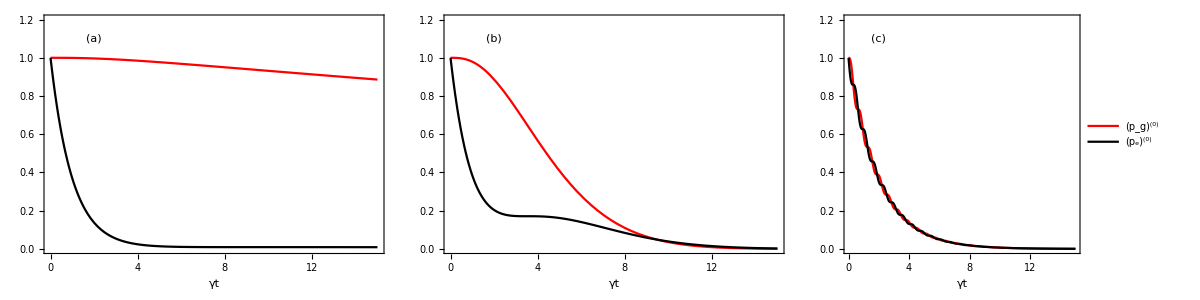

```mathematica
Module[{parameterslist},
parameterslist=listofparametersCoherentDrive;
noEmissionComponentPlot=Grid[{Table[

Plot[{p0g/.parameterslist[[k]],p0e/.parameterslist[[k]]},{t,0,15},
PlotRange->{All,{0,1.2}},
PlotStyle->{Red,{Black}},
FrameLabel->{"γt"},
PlotLegends->If[k==Length@parameterslist, legend[{"(p_g)^(0)","(p_e)^(0)"},{0.8,0.7}],None],
Epilog->Inset[alphabetlabel[[k]],{2,1.1}]
],

{k,1,Length@listofparametersCoherentDrive}]}]
]
Export[PlotsPath<>"noEmissionComponent.pdf",noEmissionComponentPlot];
```

```mathematica
coeff1photonEmissionList=
{f1eg=f1[e,g,t,t1],
f1gg=f1[g,g,t,t1],
f1ee=f1[e,e,t,t1],
f1ge=f1[g,e,t,t1]};
```

```mathematica
(*Computing the probabilities of 1 photons emission*)
Module[{aux1,aux2,aux3,aux4,aux5,aux6},

Print["Computing the 1 e→e"];
aux1=((f1ee/.δ->0//cf)(f1ee/.δ->0//cf)*)//cf;
PrettyTiming[p1ee=Integrate[aux1,{t1,0,t}]];

Print["Computing the 1 e→g"];
aux2=((f1ge/.δ->0//cf)(f1ge/.δ->0//cf)*)//cf;
PrettyTiming[p1ge=Integrate[aux2,{t1,0,t}]];

Print["Computing the 1 g→e"];
aux3=((f1eg/.δ->0//cf)(f1eg/.δ->0//cf)*)//cf;
PrettyTiming[p1eg=Integrate[aux3,{t1,0,t}]];

Print["Computing the 1 g→g"];
aux4=((f1gg/.δ->0//cf)(f1gg/.δ->0//cf)*)//cf;
PrettyTiming[p1gg=Integrate[aux4,{t1,0,t}]]
]
```

Computing the 1 e→e

0h : 1m : 20s

Computing the 1 e→g

Integrate::idiv: Integral of -2 Ω^2 Cos[1/4 t √(-Power[«2»]+4 Power[«2»])]+γ^2 Cos[1/4 (t-2 t1) √(-Power[«2»]+4 Power[«2»])]-2 «1» Cos[1/4 (t-«1») √(-Power[«2»]+4 «1»)]-γ √(-γ^2+4 Ω^2) Sin[1/4 (t-2 t1) √(-Power[«2»]+4 Power[«2»])] does not converge on {0,Integrate`ImproperDump`xx$220441}.

0h : 0m : 20s

Computing the 1 g→e

0h : 0m : 10s

Computing the 1 g→g

0h : 0m : 6s

∫_0^t 1/((γ^2-4 Ω^2)^2)4 ⅇ^(-(t γ)/2) Ω^2 Conjugate[√(-γ^2+4 Ω^2) Cos[1/4 (t-t1) √(-γ^2+4 Ω^2)]+γ Sin[1/4 (t-t1) √(-γ^2+4 Ω^2)]] (√(-γ^2+4 Ω^2) Cos[1/4 (t-t1) √(-γ^2+4 Ω^2)]+γ Sin[1/4 (t-t1) √(-γ^2+4 Ω^2)]) Sin[1/4 t1 √(-γ^2+4 Ω^2)] Sin[1/4 t1 Conjugate[√(-γ^2+4 Ω^2)]]ⅆt1

## Single-photon pulse

```mathematica
Intensity[funcoft_]:=funcoft funcoft*//cf
```

```mathematica
Clear[ξdec,γ,Γ,ω0];
ξdec[t_] := √Γ Exp[-(Γ/2+ⅈ ω0)t];
InputIntensityDec=Intensity[ξdec[t]];

Integrate[ξdec[t] ξdec[t]*//cf, {t,0,∞}]
```

ConditionalExpression[1, Re[Γ]>0]

```mathematica
Clear[ξdectilde];
ξdectilde[t_] :=ⅇ^(-(γ t)/2)Integrate[ⅇ^((γ/2+ⅈ ω0)s)ξdec[s],{s,0,t}] ;
ξdectilde[t]
```

(2 ⅇ^(-(t γ)/2) (-1+ⅇ^(1/2 t (γ-Γ))) √Γ)/(γ-Γ)

```mathematica
(*Computing the output shape*)
Υdec[t_]:=γ ξdectilde[t] ⅇ^(-ⅈ ω0 t)-ξdec[t]
OutputIntensityDec=Intensity[Υdec[t]];
Integrate[Υdec[t] Υdec[t]*//cf, {t,0,∞}]
```

ConditionalExpression[1, Re[γ]>0&&Re[Γ]>0]

```mathematica
Υdec[t]//cf
```

(ⅇ^(-1/2 t (γ+2 ⅈ ω0)) √Γ (2 γ-ⅇ^(1/2 t (γ-Γ)) (γ+Γ)))/(-γ+Γ)

```mathematica
test1=Limit[Υdec[t],Γ->γ]//cf//Quiet
test2=ξdec[t]/.Γ->γ
```

ⅇ^(t (-1/2-ⅈ ω0)) (-1+t)

ⅇ^(t (-1/2-ⅈ ω0))